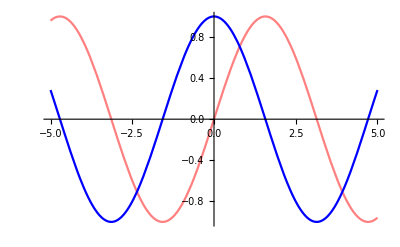

```mathematica
Plot[{Sin[x], Cos[x]},{x, -5, 5}, PlotStyle->{Pink, Blue}]
```

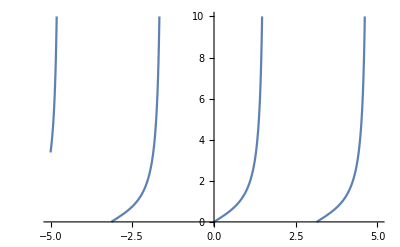

```mathematica
Plot[Tan[x],{x, -5, 5}, PlotRange->{0, 10}]
```

```mathematica
a = 0.1;
R[phi_] := Exp[a*phi];
```

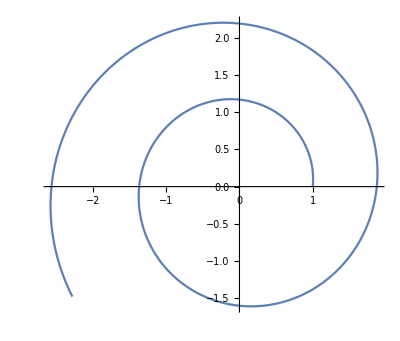

```mathematica
PolarPlot[R[phi], {phi, 0, 10}]
```

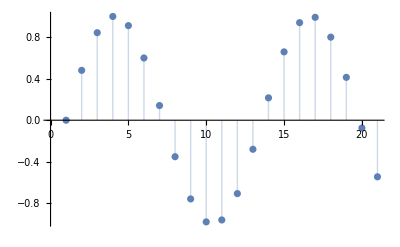

```mathematica
t = Table[Sin[x],{x,0,10, 1/2}];
ListPlot[t, Filling->Axis]
```

```mathematica
lm=LinearModelFit[t,Table[x^i, {i, 0, 6}],x]
```

FittedModel[-0.239731-0.0441797 x+0.380808 x^2-0.111861 x^3+0.0116962 x^4-0.000516261 x^5+8.19031×10^-6 x^6]

```mathematica
te=Map[Function[x,{x, 1/10}],t];
```

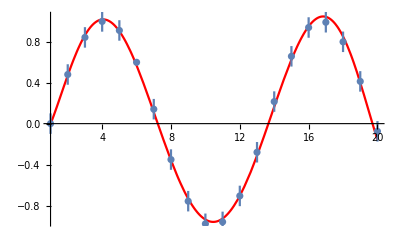

```mathematica
Needs["ErrorBarPlots`"];
Show[Plot[lm[x],{x,1,20}, PlotStyle->Red], ErrorListPlot[te]]
```

```mathematica
z = Sin[r]/r
```

Sin[r]/r

```mathematica
r=Sqrt[x^2+y^2]
```

√(x^2+y^2)

```mathematica
Plot3D[z,{x, -10, 10}, {y, -10, 10}, Mesh->30, PlotPoints->50, PlotRange->Full]
```

-Graphics3D-

```mathematica
a = 2;
b = 1;
A[v_] := a + b*Sin[v];
ParametricPlot3D[{A[v]*Cos[u],A[v]*Sin[u],b*Cos[v]}, {u, 0, 2*Pi}, {v, 0, 2*Pi}]
```

-Graphics3D-

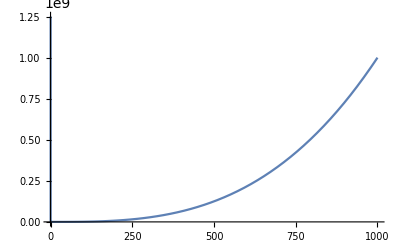

```mathematica
Plot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

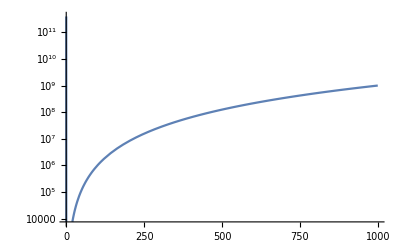

```mathematica
LogPlot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

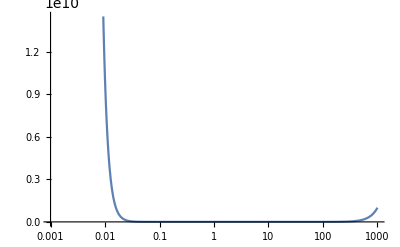

```mathematica
LogLinearPlot[x^3 + x^(-5), {x, 10^(-3), 10^3}]
```

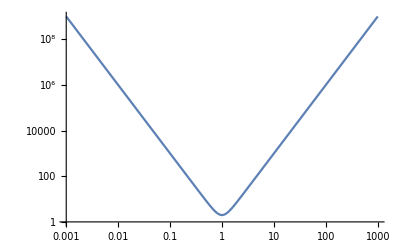

```mathematica
LogLogPlot[x^3+x^(-3),{x,10^(-3),10^3}]
```